```mathematica
Clear[Lx,Ly,A,B,
sx2d,SX2D,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=16;
Ly=16;
midPtX = Floor[Lx/2];
midPtY = Floor[Ly/2];
A=Lx*Ly;
Lz=20;
```

```mathematica
B=0.1;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2 Exp[- I B],sy2d[(k+1)Lx+j,k Lx+j]=I/2 Exp[ I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2 Exp[- I B],cy2d[(k+1)Lx+j,k Lx+j]=1/2 Exp[I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1, HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_, αy_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

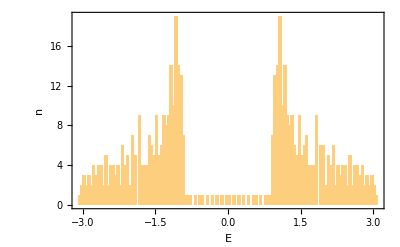

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,Lz-1]
```

{-3.14159,-2.8109,-2.4802,-2.14951,-1.81882,-1.48812,-1.15743,-0.826735,-0.496041,-0.165347,0.165347,0.496041,0.826735,1.15743,1.48812,1.81882,2.14951,2.4802,2.8109,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

20

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[SitesWithMagFieldInside,Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

512

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
SitesWithMagFieldInside = {{midPtX,midPtY},{midPtX+1,midPtY},{midPtX+1,midPtY+1},{midPtX,midPtY+1},{midPtX,midPtY}};
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/(1+Sqrt[5]))*(x-1)+5
LineDn[x_]:=(2/(1+Sqrt[5]))*(x-2)+3
```

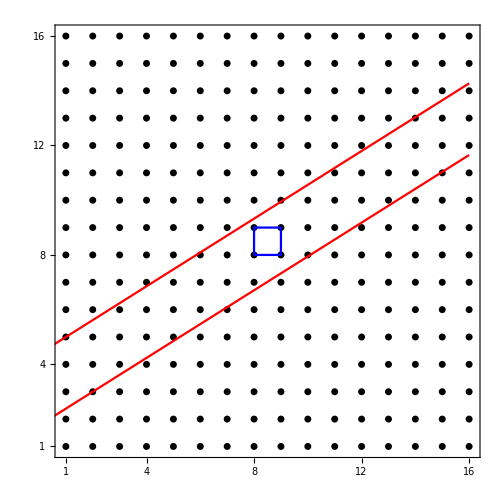

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[SitesWithMagFieldInside,PlotStyle-> {Blue,PointSize[0.01]},Joined-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{81,97,98,99,114,115,116,131,132,133,134,149,150,151,166,167,168,169,184,185,186,201,202,203,204,219,220,221,236,237,238,239,254,255,256}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{161,162,193,194,195,196,197,198,227,228,229,230,231,232,261,262,263,264,265,266,267,268,297,298,299,300,301,302,331,332,333,334,335,336,337,338,367,368,369,370,371,372,401,402,403,404,405,406,407,408,437,438,439,440,441,442,471,472,473,474,475,476,477,478,507,508,509,510,511,512}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

70

```mathematica
NOrbitalsQuasi/2
```

35

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

442

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.136719

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{512}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(** Mixed boundary **)
```

```mathematica
Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM1[1,1,0,1,kzVector[[i]],1]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]
```

```mathematica
bb = Sort[Re[bb]];
```

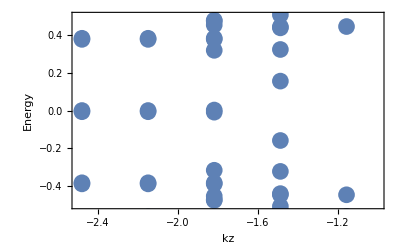

```mathematica
Show[ListPlot[bb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.03]],AxesLabel-> {"kz","Energy"},Frame-> True]
```

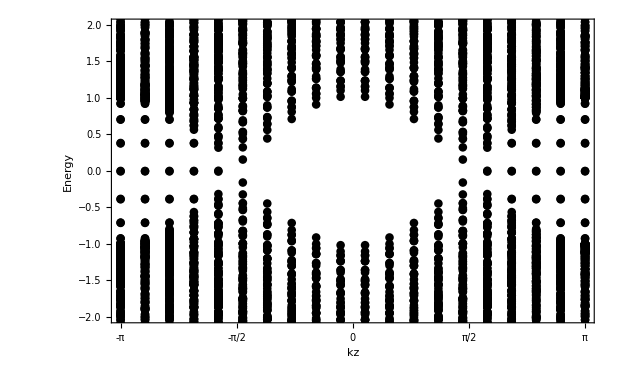

```mathematica
Plot1=Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->{PointSize[0.01],Black}],FrameLabel-> {"kz","Energy"},BaseStyle-> 18,Frame-> True,FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}}]
```

```mathematica
(** Calculate Charge density as a function of position **)
```

```mathematica
Clear[ChargeXY, ChargeXYFlatten, ChargeXYPlot]
```

```mathematica
ChargeXY = Table[{x,y,0},{x,1,Lx},{y,1,Ly}];
```

```mathematica
Dimensions[ChargeXY]
```

{16,16,3}

```mathematica
Do[{Clear[HTrial,ValueFibon,VecFibon,ValFibon,OnlyEigenvalue,ValVecFibon],
HTrial =HamiltonianWSM1[1,1,0,1,kzVector[[kzIndex]],1],
{ValueFibon,VecFibon}=Eigensystem[HTrial],
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First],
Do[Do[Do[ChargeXY[[x,y]][[3]] += Abs[ValVecFibon[[J,2,2(x + (y-1)Lx)]]]^2+Abs[ValVecFibon[[J,2,2(x + (y-1)Lx)-1]]]^2,{x,1,Lx}],{y,1,Ly}],{J,1,A}]},{kzIndex ,1,Lz}];
```

```mathematica
ChargeXY;
```

```mathematica
ChargeXYFlatten = Flatten[ChargeXY];
```

```mathematica
Dimensions[ChargeXYFlatten][[1]]
```

768

```mathematica
Lx*Ly*3
```

768

```mathematica
ChargeXYFlatten[[18]]
```

19.751

```mathematica
ChargeXYPlot = Table[{ChargeXYFlatten[[3i-2]],ChargeXYFlatten[[3i-1]],ChargeXYFlatten[[3i]]},{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{{1,1,19.751},{1,2,19.751},{1,3,19.751},{1,4,19.751},{1,5,19.751},{1,6,19.751},{1,7,19.751},{1,8,19.751},{1,9,19.751},{1,10,19.751},{1,11,19.751},{1,12,19.751},{1,13,19.751},{1,14,19.751},{1,15,19.751},{1,16,19.751},{2,1,19.9785},{2,2,19.9785},{2,3,19.9785},{2,4,19.9785},{2,5,19.9785},{2,6,19.9785},{2,7,19.9785},{2,8,19.9785},{2,9,19.9785},{2,10,19.9785},{2,11,19.9785},{2,12,19.9785},{2,13,19.9785},{2,14,19.9785},{2,15,19.9785},{2,16,19.9785},{3,1,19.993},{3,2,19.993},{3,3,19.993},{3,4,19.993},{3,5,19.993},{3,6,19.993},{3,7,19.993},{3,8,19.993},{3,9,19.993},{3,10,19.993},{3,11,19.993},{3,12,19.993},{3,13,19.993},{3,14,19.993},{3,15,19.993},{3,16,19.993},{4,1,19.9968},{4,2,19.9968},{4,3,19.9968},{4,4,19.9968},{4,5,19.9968},{4,6,19.9968},{4,7,19.9968},{4,8,19.9968},{4,9,19.9968},{4,10,19.9968},{4,11,19.9968},{4,12,19.9968},{4,13,19.9968},{4,14,19.9968},{4,15,19.9968},{4,16,19.9968},{5,1,19.9983},{5,2,19.9983},{5,3,19.9983},{5,4,19.9983},{5,5,19.9983},{5,6,19.9983},{5,7,19.9983},{5,8,19.9983},{5,9,19.9984},{5,10,19.9984},{5,11,19.9983},{5,12,19.9983},{5,13,19.9983},{5,14,19.9983},{5,15,19.9983},{5,16,19.9983},{6,1,19.9991},{6,2,19.9991},{6,3,19.9991},{6,4,19.9991},{6,5,19.9991},{6,6,19.9991},{6,7,19.9991},{6,8,19.9992},{6,9,19.9995},{6,10,19.9995},{6,11,19.9992},{6,12,19.9991},{6,13,19.9991},{6,14,19.9991},{6,15,19.9991},{6,16,19.9991},{7,1,19.9995},{7,2,19.9995},{7,3,19.9995},{7,4,19.9995},{7,5,19.9995},{7,6,19.9995},{7,7,19.9996},{7,8,19.9999},{7,9,20.0022},{7,10,20.0022},{7,11,19.9999},{7,12,19.9996},{7,13,19.9995},{7,14,19.9995},{7,15,19.9995},{7,16,19.9995},{8,1,19.9998},{8,2,19.9998},{8,3,19.9998},{8,4,19.9998},{8,5,19.9998},{8,6,19.9999},{8,7,20.0002},{8,8,20.0025},{8,9,20.0334},{8,10,20.0334},{8,11,20.0025},{8,12,20.0002},{8,13,19.9999},{8,14,19.9998},{8,15,19.9998},{8,16,19.9998},{9,1,20.0001},{9,2,20.0001},{9,3,20.0001},{9,4,20.0001},{9,5,20.0001},{9,6,20.0001},{9,7,20.0004},{9,8,20.0027},{9,9,20.0337},{9,10,20.0337},{9,11,20.0027},{9,12,20.0004},{9,13,20.0001},{9,14,20.0001},{9,15,20.0001},{9,16,20.0001},{10,1,20.0004},{10,2,20.0004},{10,3,20.0004},{10,4,20.0004},{10,5,20.0004},{10,6,20.0004},{10,7,20.0004},{10,8,20.0007},{10,9,20.003},{10,10,20.003},{10,11,20.0007},{10,12,20.0004},{10,13,20.0004},{10,14,20.0004},{10,15,20.0004},{10,16,20.0004},{11,1,20.0008},{11,2,20.0008},{11,3,20.0008},{11,4,20.0008},{11,5,20.0008},{11,6,20.0008},{11,7,20.0008},{11,8,20.0009},{11,9,20.0012},{11,10,20.0012},{11,11,20.0009},{11,12,20.0008},{11,13,20.0008},{11,14,20.0008},{11,15,20.0008},{11,16,20.0008},{12,1,20.0015},{12,2,20.0015},{12,3,20.0015},{12,4,20.0015},{12,5,20.0015},{12,6,20.0015},{12,7,20.0015},{12,8,20.0015},{12,9,20.0016},{12,10,20.0016},{12,11,20.0015},{12,12,20.0015},{12,13,20.0015},{12,14,20.0015},{12,15,20.0015},{12,16,20.0015},{13,1,20.003},{13,2,20.003},{13,3,20.003},{13,4,20.003},{13,5,20.003},{13,6,20.003},{13,7,20.003},{13,8,20.003},{13,9,20.003},{13,10,20.003},{13,11,20.003},{13,12,20.003},{13,13,20.003},{13,14,20.003},{13,15,20.003},{13,16,20.003},{14,1,20.0067},{14,2,20.0067},{14,3,20.0067},{14,4,20.0067},{14,5,20.0067},{14,6,20.0067},{14,7,20.0067},{14,8,20.0067},{14,9,20.0067},{14,10,20.0067},{14,11,20.0067},{14,12,20.0067},{14,13,20.0067},{14,14,20.0067},{14,15,20.0067},{14,16,20.0067},{15,1,20.0206},{15,2,20.0206},{15,3,20.0206},{15,4,20.0206},{15,5,20.0206},{15,6,20.0206},{15,7,20.0206},{15,8,20.0206},{15,9,20.0206},{15,10,20.0206},{15,11,20.0206},{15,12,20.0206},{15,13,20.0206},{15,14,20.0206},{15,15,20.0206},{15,16,20.0206},{16,1,20.2409},{16,2,20.2409},{16,3,20.2409},{16,4,20.2409},{16,5,20.2409},{16,6,20.2409},{16,7,20.2408},{16,8,20.2408},{16,9,20.2408},{16,10,20.2408},{16,11,20.2408},{16,12,20.2408},{16,13,20.2409},{16,14,20.2409},{16,15,20.2409},{16,16,20.2409}}

```mathematica
ChargeXYPlotData = Table[ChargeXYFlatten[[3i]],{i,1,Dimensions[ChargeXYFlatten][[1]]/3}]
```

{19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.751,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.9785,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.993,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9968,19.9983,19.9983,19.9983,19.9983,19.9983,19.9983,19.9983,19.9983,19.9984,19.9984,19.9983,19.9983,19.9983,19.9983,19.9983,19.9983,19.9991,19.9991,19.9991,19.9991,19.9991,19.9991,19.9991,19.9992,19.9995,19.9995,19.9992,19.9991,19.9991,19.9991,19.9991,19.9991,19.9995,19.9995,19.9995,19.9995,19.9995,19.9995,19.9996,19.9999,20.0022,20.0022,19.9999,19.9996,19.9995,19.9995,19.9995,19.9995,19.9998,19.9998,19.9998,19.9998,19.9998,19.9999,20.0002,20.0025,20.0334,20.0334,20.0025,20.0002,19.9999,19.9998,19.9998,19.9998,20.0001,20.0001,20.0001,20.0001,20.0001,20.0001,20.0004,20.0027,20.0337,20.0337,20.0027,20.0004,20.0001,20.0001,20.0001,20.0001,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0004,20.0007,20.003,20.003,20.0007,20.0004,20.0004,20.0004,20.0004,20.0004,20.0008,20.0008,20.0008,20.0008,20.0008,20.0008,20.0008,20.0009,20.0012,20.0012,20.0009,20.0008,20.0008,20.0008,20.0008,20.0008,20.0015,20.0015,20.0015,20.0015,20.0015,20.0015,20.0015,20.0015,20.0016,20.0016,20.0015,20.0015,20.0015,20.0015,20.0015,20.0015,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.003,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0067,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.0206,20.2409,20.2409,20.2409,20.2409,20.2409,20.2409,20.2408,20.2408,20.2408,20.2408,20.2408,20.2408,20.2409,20.2409,20.2409,20.2409}

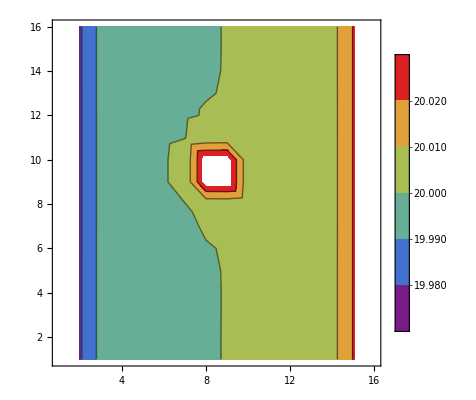

```mathematica
ListContourPlot[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
ListPlot3D[ChargeXYPlot,PlotRange->{{1,Lx},{1,Ly}},PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** to measure in the unit of e/π, we multiply with π **)
```

```mathematica
deltaQ = π * Sum[(ChargeXY[[x,y]][[3]])/Lz,{x,midPtX-1,midPtX+2},{y,1,Ly}]
```

201.086

```mathematica
dataQ = {{0,N[64*π]},{0.01, 201.064370710888},{0.02,201.0668117637175},{0.03,201.069253148827},{0.04,201.07169500657213 },{0.05,201.07413745039446},{0.07,201.07902439823897},{0.1,201.08636035993376}}
```

{{0,201.062},{0.01,201.064},{0.02,201.067},{0.03,201.069},{0.04,201.072},{0.05,201.074},{0.07,201.079},{0.1,201.086}}

```mathematica
Dimensions[dataQ][[1]]
```

8

```mathematica
dataDeltaQ = Table[{dataQ [[i]][[1]],dataQ [[i]][[2]] - dataQ [[1]][[2]]},{i,1,Dimensions[dataQ][[1]]}]
```

{{0,0.},{0.01,0.00244088},{0.02,0.00488193},{0.03,0.00732332},{0.04,0.00976518},{0.05,0.0122076},{0.07,0.0170946},{0.1,0.0244305}}

```mathematica
Fit[dataDeltaQ,{x},x]
```

0.244236 x

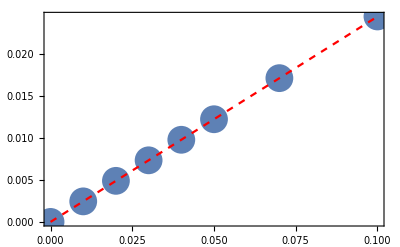

```mathematica
Show[ListPlot[dataDeltaQ,PlotStyle->PointSize[0.05]],Plot[0.24416874645085007 x,{x,0,0.1},PlotStyle->{Dashed,Red}],Frame->True,BaseStyle->18,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(** magnetic field 0.1 -> 64.04897097607557 **)
```

```mathematica
(** magnetic field 0.3 -> delta Q 64.14492972147679 **)
```

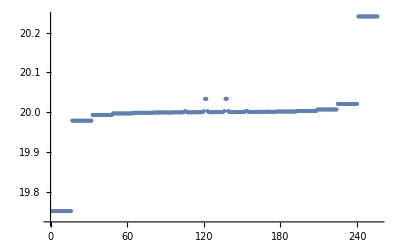

```mathematica
ListPlot[Transpose@{Table[i,{i,1,Lx*Ly}],ChargeXYPlotData},PlotRange->All]
```